# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box diagrams with GAUGE=1

Confronto con:
- EW_MM_naive per d=4 -> OK
-Nar per d (box photons and born Z) CON SEMPLIFICAZIONE CARICHE PRIMA DEL CALCOLO DELLE TRACCE

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

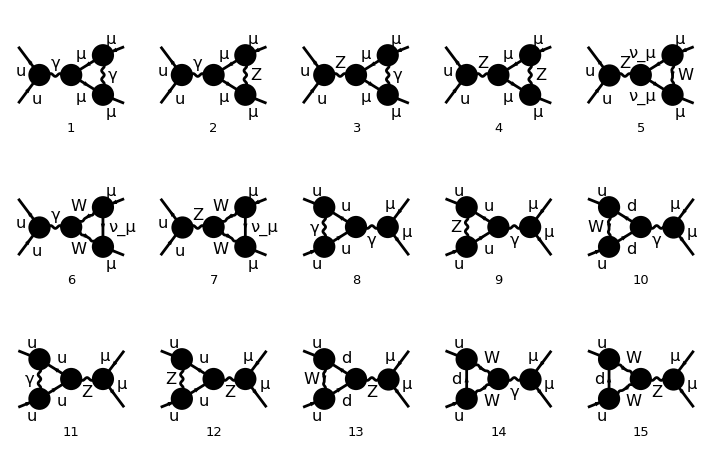

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

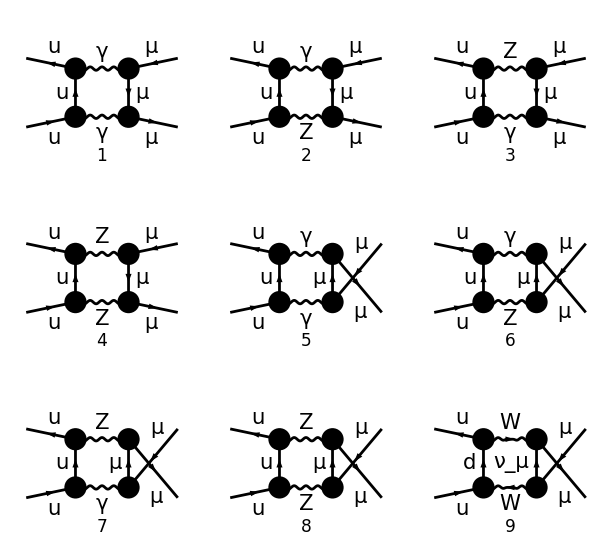

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

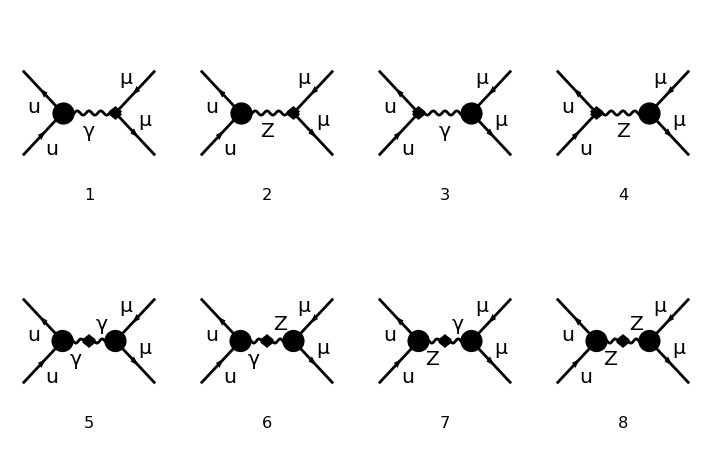

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[3][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[3][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
(*tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];*)
```

```mathematica
(*confronto Nar*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[-(p1)+q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,0].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).gs[q1-k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k1,0] FeynAmpDenominator[1/(p1-q1)^2,1/(p1+p2-q1)^2,1/(-MZ2+(q1)^2),1/(-(q1)+k1)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[p2-q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,0].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).gs[q1-k1].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).v[k1,0] FeynAmpDenominator[1/(p2-q1)^2,1/(-MZ2+(p1+p2-q1)^2),1/(q1)^2,1/(-(q1)+k1)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.NonCommutative[DiracMatrix[Index[Lorentz,bn1_]],ChiralityProjector[n_]]->NonCommutative[ChiralityProjector[n],DiracMatrix[Index[Lorentz,bn1]]]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=bornpropag//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(ⅈ EL QUl om_-.ga[Lorbn1]+ⅈ EL QUr om_+.ga[Lorbn1]).u[p1,0]],CONJ[ū[k1,0].(ⅈ EL QLl om_-.ga[Lorbn2]+ⅈ EL QLr om_+.ga[Lorbn2]).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

#### colour trace

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Propagators

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
bornpropag2
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (p1-q1)^2 (p1+p2-q1)^2 (-MZ2+(q1)^2) (q1-k1)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p2-q1)^2 (q1)^2 (q1-k1)^2)

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
D1=1/List@@Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
```

```mathematica
D2=1/List@@Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
```

```mathematica
intdenT[expr_]:=Module[{t,t1,A1},

dennnt=Sort[Table[If[Head[D1[[i]]]===Power,D1[[i,1]]->Sqrt[dn[i]],D1[[i]]->dn[i]],{i,1,Length[D1]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D1]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];
t=ReplaceAllRestricted[expr,dennnt,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENt@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D1]}],{j,1,Length[t]}],
expon=DENt@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D1]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];


intdenU[expr_]:=Module[{t,t1,A2},

dennnu=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnu,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENu@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENu@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
intdenU[unumerat*bornpropag2]
```

(ⅈ DENu[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(16 π^4 S)

```mathematica
intdenT[tnumerat*bornpropag2]
```

(ⅈ DENt[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(16 π^4 S)

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
SP/: SP[P1,K1]:=(-T)/2;
SP/: SP[P2,K2]:=(-T)/2; 
SP/:SP[P1,K2]:=(-U)/2; SP/:SP[P2,K1]:=(-U)/2;
```

```mathematica
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracMatrix[b],y]/;Head[b]=!=FourMomentum;
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracSlash[b],y]/;Head[b]===FourMomentum;
```

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] :=Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=0;
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=0;
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
```

```mathematica
LARINtot:= traceff4[x___,G5,y___]:>LARIN[ traceff4[x,G5,y] ];
```

```mathematica
LARIN[expr_]:=Module[{ris,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12},
a1 = Index[Lorentz,Unique["x"]];
a2 = Index[Lorentz,Unique["x"]];
a3 = Index[Lorentz,Unique["x"]];
a4 = Index[Lorentz,Unique["x"]];
a5 = Index[Lorentz,Unique["x"]];
a6 = Index[Lorentz,Unique["x"]];
a7= Index[Lorentz,Unique["x"]];
a8 = Index[Lorentz,Unique["x"]];
a9 = Index[Lorentz,Unique["x"]];
a10 = Index[Lorentz,Unique["x"]];
a11 = Index[Lorentz,Unique["x"]];
a12 = Index[Lorentz,Unique["x"]];

pos = Position[ expr, G5];
Which[Length[pos]===1,
pos1 = Position[ expr, G5][[1,1]];
ris = I/24 fg51 myEps[a1,a2,a3,a4]*ReplacePart[expr,pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]] ],
Length[pos]===2,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
ris = (I/24)^2 fg52 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]]} ],
Length[pos]===3,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
pos3 = Position[ expr, G5][[3,1]];
(*cambiare MYEPS in myEps per verificare i prodotti con 3 levicivita,ovvero conta l'ordine dei prodotti?*)
ris = (I/24)^3 fg53 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*myEps[a9,a10,a11,a12]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]],pos3->Sequence[DiracMatrix[a9],DiracMatrix[a10],DiracMatrix[a11],DiracMatrix[a12]]} ]
];

ris					   
];
```

```mathematica
(*semplificazione propagatore stato f*)
SEMPLtr={traceff4[a___,p[MM+DiracSlash[b__]],c___]/;OddQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,DiracSlash[b],c],
traceff4[a___,p[MM+DiracSlash[b__]],c___]/;EvenQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,MM,c]};
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{i,tr1i,tr2i,tr3i,tr4i,tr1f,tr2f,tr3f,tr4f,tracciai,tracciaf,chii,chff,omi,omf},

(*Prova traceff con mom k1 e p1 >0 v vbar->p-m uubar->p+m*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,1,b___]:=traceff4[a,b];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

(*stato i*)
omi=Count[statoi[[1]],_ChiralityProjector,Infinity];
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}];
tr2i=Map[Distribute,1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
tr2i=tr2i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)

tr3i=Collect[Collect[tr2i,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4i=tr3i//.TR->myTr;

Print["stato i ",1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
omf=Count[statof[[1]],_ChiralityProjector,Infinity];
tr1f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.SEMPLtr;
tr2f=Flatten[Map[Distribute,1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]];

tr2f=tr2f*chargetot[[2]]//.List->Plus//Simplify;(*prova*)

tr3f=Collect[Collect[tr2f,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4f=tr3f//.TR->myTr;

Print["stato f ",1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr4i,tr4f}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_,conjbornchains_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbi2=tbi(*Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List*);(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
stati=stati//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[tbf[[i]]/.MM+DiracSlash[a__]->p[MM+DiracSlash[a]]//.List->f,{i,1,Length[tbf]}],Plus->Sequence,{3},Heads->True]//.f->List;
tbf3=DeleteCases[tbf2,0,1];
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
statf=statf//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

#### CHARGES

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[Q1,Q1]->Q1^2};
```

```mathematica
(*per calcolare altri box con photon/Z(caso boxtt o incrociato boxuu) o W(boxuu) basta cambiare la cariche, essendo le tracce della stessa tipologia*)
```

#### amplitudes

```mathematica
boxtt=traces[fermiontrace[tboxzz,conjbornchains][[1]],fermiontrace[tboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]}}

```mathematica
boxuu=traces[fermiontrace[uboxzz,conjbornchains][[1]],fermiontrace[uboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]}}

## Simplifications

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
```

#### myEps

```mathematica
Tepsi=iep*tnumerat*bornpropag2//.{MM->0,MM2->0}//Expand;
```

```mathematica
Teps=ParallelSum[Tepsi*fep[[j]]//Expand,{j,1,Length[fep]}];
```

```mathematica
Teps2=Collect[Teps//.{fg51->1,fg53->1},_SP,Simplify];
```

```mathematica
Teps1=Collect[Teps//.{fg51->1,fg53->1},_SP,Simplify];
```

```mathematica
Collect[Teps1[[1]]*TT1-
TT2*Teps2[[1]]//.U->-S-T,d,Simplify]
```

(ⅈ Alfa Alfa2 d^9 I3L^3 I3U^3 S T (41 S TT1+82 T TT1+37 S TT2+4 T TT2) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^8 I3L^3 I3U^3 S T (187 S TT1+370 T TT1+146 S TT2+31 T TT2) DENt[1,1,1,1])/(288 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^10 I3L^3 I3U^3 S T (2 T TT1+S (TT1+TT2)) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)+(ⅈ Alfa Alfa2 d^7 I3L I3U^3 S T (-48 I3L QL S SW2 TT2+48 QL^2 S SW2^2 TT2+I3L^2 (7786 T TT1+796 T TT2+7 S (571 TT1+371 TT2))) DENt[1,1,1,1])/(576 CW2^3 π (MZ2-S) SW2^3)-1/(CW2^3 π (MZ2-S) SW2^3)3 ⅈ Alfa Alfa2 I3L I3U S T (4 I3L QL SW2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))-4 QL^2 SW2^2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))+I3L^2 (4 I3U QU SW2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)-4 QU^2 SW2^2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)+I3U^2 (161 S TT1+366 T TT1+15 S TT2+10 T TT2))) DENt[1,1,1,1]+1/(CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d I3L I3U S T (-I3L QL SW2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+QL^2 SW2^2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+I3L^2 (I3U QU SW2 (33 S TT1-566 T TT1+101 S TT2-62 T TT2)+QU^2 SW2^2 (-33 S TT1+566 T TT1-101 S TT2+62 T TT2)+I3U^2 (1545 S TT1+3143 T TT1+196 S TT2+157 T TT2))) DENt[1,1,1,1]-1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^6 I3L I3U S T (-96 I3L I3U^2 QL SW2 (4 T (TT1+TT2)+S (TT1+24 TT2))+96 I3U^2 QL^2 SW2^2 (4 T (TT1+TT2)+S (TT1+24 TT2))+I3L^2 (-96 I3U QU SW2 (S+4 T) (TT1+TT2)+96 QU^2 SW2^2 (S+4 T) (TT1+TT2)+I3U^2 (55405 S TT1+106042 T TT1+29021 S TT2+11320 T TT2))) DENt[1,1,1,1]-1/(48 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^2 I3L I3U S T (-16 I3L QL SW2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+16 QL^2 SW2^2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+I3L^2 (-16 I3U QU SW2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+16 QU^2 SW2^2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+I3U^2 (97969 S TT1+188578 T TT1+17935 S TT2+13274 T TT2))) DENt[1,1,1,1]+1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^5 I3L I3U S T (-96 I3L I3U^2 QL SW2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+96 I3U^2 QL^2 SW2^2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+I3L^2 (-288 I3U QU SW2 (5 S+24 T) (TT1+TT2)+288 QU^2 SW2^2 (5 S+24 T) (TT1+TT2)+I3U^2 (259265 S TT1+488450 T TT1+107221 S TT2+50372 T TT2))) DENt[1,1,1,1]+1/(288 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^3 I3L I3U S T (-24 I3L QL SW2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+24 QL^2 SW2^2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+I3L^2 (-72 I3U QU SW2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+72 QU^2 SW2^2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+I3U^2 (437751 S TT1+821782 T TT1+108111 S TT2+69664 T TT2))) DENt[1,1,1,1]-1/(576 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^4 I3L I3U S T (48 I3L I3U^2 QL SW2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))-48 I3U^2 QL^2 SW2^2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))+I3L^2 (-48 I3U QU SW2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+48 QU^2 SW2^2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+I3U^2 (412551 S TT1+770662 T TT1+132857 S TT2+73454 T TT2))) DENt[1,1,1,1]

```mathematica
teps1=(ⅈ Alfa Alfa2 d^9 I3L^3 I3U^3 S T (41 S TT1+82 T TT1+37 S TT2+4 T TT2) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^8 I3L^3 I3U^3 S T (187 S TT1+370 T TT1+146 S TT2+31 T TT2) DENt[1,1,1,1])/(288 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^10 I3L^3 I3U^3 S T (2 T TT1+S (TT1+TT2)) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)+(ⅈ Alfa Alfa2 d^7 I3L I3U^3 S T (-48 I3L QL S SW2 TT2+48 QL^2 S SW2^2 TT2+I3L^2 (7786 T TT1+796 T TT2+7 S (571 TT1+371 TT2))) DENt[1,1,1,1])/(576 CW2^3 π (MZ2-S) SW2^3)-1/(CW2^3 π (MZ2-S) SW2^3)3 ⅈ Alfa Alfa2 I3L I3U S T (4 I3L QL SW2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))-4 QL^2 SW2^2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))+I3L^2 (4 I3U QU SW2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)-4 QU^2 SW2^2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)+I3U^2 (161 S TT1+366 T TT1+15 S TT2+10 T TT2))) DENt[1,1,1,1]+1/(CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d I3L I3U S T (-I3L QL SW2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+QL^2 SW2^2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+I3L^2 (I3U QU SW2 (33 S TT1-566 T TT1+101 S TT2-62 T TT2)+QU^2 SW2^2 (-33 S TT1+566 T TT1-101 S TT2+62 T TT2)+I3U^2 (1545 S TT1+3143 T TT1+196 S TT2+157 T TT2))) DENt[1,1,1,1]-1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^6 I3L I3U S T (-96 I3L I3U^2 QL SW2 (4 T (TT1+TT2)+S (TT1+24 TT2))+96 I3U^2 QL^2 SW2^2 (4 T (TT1+TT2)+S (TT1+24 TT2))+I3L^2 (-96 I3U QU SW2 (S+4 T) (TT1+TT2)+96 QU^2 SW2^2 (S+4 T) (TT1+TT2)+I3U^2 (55405 S TT1+106042 T TT1+29021 S TT2+11320 T TT2))) DENt[1,1,1,1]-1/(48 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^2 I3L I3U S T (-16 I3L QL SW2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+16 QL^2 SW2^2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+I3L^2 (-16 I3U QU SW2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+16 QU^2 SW2^2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+I3U^2 (97969 S TT1+188578 T TT1+17935 S TT2+13274 T TT2))) DENt[1,1,1,1]+1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^5 I3L I3U S T (-96 I3L I3U^2 QL SW2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+96 I3U^2 QL^2 SW2^2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+I3L^2 (-288 I3U QU SW2 (5 S+24 T) (TT1+TT2)+288 QU^2 SW2^2 (5 S+24 T) (TT1+TT2)+I3U^2 (259265 S TT1+488450 T TT1+107221 S TT2+50372 T TT2))) DENt[1,1,1,1]+1/(288 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^3 I3L I3U S T (-24 I3L QL SW2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+24 QL^2 SW2^2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+I3L^2 (-72 I3U QU SW2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+72 QU^2 SW2^2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+I3U^2 (437751 S TT1+821782 T TT1+108111 S TT2+69664 T TT2))) DENt[1,1,1,1]-1/(576 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^4 I3L I3U S T (48 I3L I3U^2 QL SW2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))-48 I3U^2 QL^2 SW2^2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))+I3L^2 (-48 I3U QU SW2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+48 QU^2 SW2^2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+I3U^2 (412551 S TT1+770662 T TT1+132857 S TT2+73454 T TT2))) DENt[1,1,1,1]//.TT2->0//.TT1->1;
```

```mathematica
teps2=(ⅈ Alfa Alfa2 d^9 I3L^3 I3U^3 S T (41 S TT1+82 T TT1+37 S TT2+4 T TT2) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^8 I3L^3 I3U^3 S T (187 S TT1+370 T TT1+146 S TT2+31 T TT2) DENt[1,1,1,1])/(288 CW2^3 π (MZ2-S) SW2^3)-(ⅈ Alfa Alfa2 d^10 I3L^3 I3U^3 S T (2 T TT1+S (TT1+TT2)) DENt[1,1,1,1])/(1152 CW2^3 π (MZ2-S) SW2^3)+(ⅈ Alfa Alfa2 d^7 I3L I3U^3 S T (-48 I3L QL S SW2 TT2+48 QL^2 S SW2^2 TT2+I3L^2 (7786 T TT1+796 T TT2+7 S (571 TT1+371 TT2))) DENt[1,1,1,1])/(576 CW2^3 π (MZ2-S) SW2^3)-1/(CW2^3 π (MZ2-S) SW2^3)3 ⅈ Alfa Alfa2 I3L I3U S T (4 I3L QL SW2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))-4 QL^2 SW2^2 (4 I3U QU SW2 (S+6 T) (TT1-TT2)-4 QU^2 SW2^2 (S+6 T) (TT1-TT2)+I3U^2 (23 S TT1-30 T TT1-5 S TT2+2 T TT2))+I3L^2 (4 I3U QU SW2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)-4 QU^2 SW2^2 (7 S TT1-22 T TT1+3 S TT2+2 T TT2)+I3U^2 (161 S TT1+366 T TT1+15 S TT2+10 T TT2))) DENt[1,1,1,1]+1/(CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d I3L I3U S T (-I3L QL SW2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+QL^2 SW2^2 (-8 I3U QU SW2 (29 S+48 T) (TT1-TT2)+8 QU^2 SW2^2 (29 S+48 T) (TT1-TT2)+I3U^2 (-353 S TT1+798 T TT1+191 S TT2+62 T TT2))+I3L^2 (I3U QU SW2 (33 S TT1-566 T TT1+101 S TT2-62 T TT2)+QU^2 SW2^2 (-33 S TT1+566 T TT1-101 S TT2+62 T TT2)+I3U^2 (1545 S TT1+3143 T TT1+196 S TT2+157 T TT2))) DENt[1,1,1,1]-1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^6 I3L I3U S T (-96 I3L I3U^2 QL SW2 (4 T (TT1+TT2)+S (TT1+24 TT2))+96 I3U^2 QL^2 SW2^2 (4 T (TT1+TT2)+S (TT1+24 TT2))+I3L^2 (-96 I3U QU SW2 (S+4 T) (TT1+TT2)+96 QU^2 SW2^2 (S+4 T) (TT1+TT2)+I3U^2 (55405 S TT1+106042 T TT1+29021 S TT2+11320 T TT2))) DENt[1,1,1,1]-1/(48 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^2 I3L I3U S T (-16 I3L QL SW2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+16 QL^2 SW2^2 (-288 I3U QU SW2 (S+T) (TT1-TT2)+288 QU^2 SW2^2 (S+T) (TT1-TT2)+I3U^2 (-579 S TT1+1989 T TT1+948 S TT2+529 T TT2))+I3L^2 (-16 I3U QU SW2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+16 QU^2 SW2^2 (49 S TT1+1369 T TT1-125 S TT2+529 T TT2)+I3U^2 (97969 S TT1+188578 T TT1+17935 S TT2+13274 T TT2))) DENt[1,1,1,1]+1/(1152 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^5 I3L I3U S T (-96 I3L I3U^2 QL SW2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+96 I3U^2 QL^2 SW2^2 (7 S TT1+88 T TT1+226 S TT2+72 T TT2)+I3L^2 (-288 I3U QU SW2 (5 S+24 T) (TT1+TT2)+288 QU^2 SW2^2 (5 S+24 T) (TT1+TT2)+I3U^2 (259265 S TT1+488450 T TT1+107221 S TT2+50372 T TT2))) DENt[1,1,1,1]+1/(288 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^3 I3L I3U S T (-24 I3L QL SW2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+24 QL^2 SW2^2 (-96 I3U QU S SW2 (TT1-TT2)+96 QU^2 S SW2^2 (TT1-TT2)+I3U^2 (-571 S TT1+3392 T TT1+2809 S TT2+1488 T TT2))+I3L^2 (-72 I3U QU SW2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+72 QU^2 SW2^2 (79 S TT1+784 T TT1+15 S TT2+496 T TT2)+I3U^2 (437751 S TT1+821782 T TT1+108111 S TT2+69664 T TT2))) DENt[1,1,1,1]-1/(576 CW2^3 π (MZ2-S) SW2^3)ⅈ Alfa Alfa2 d^4 I3L I3U S T (48 I3L I3U^2 QL SW2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))-48 I3U^2 QL^2 SW2^2 (S (37 TT1-1080 TT2)-8 T (97 TT1+59 TT2))+I3L^2 (-48 I3U QU SW2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+48 QU^2 SW2^2 (91 S TT1+568 T TT1+67 S TT2+472 T TT2)+I3U^2 (412551 S TT1+770662 T TT1+132857 S TT2+73454 T TT2))) DENt[1,1,1,1]//.TT1->0//.TT2->-1;
```

```mathematica
Collect[teps1-teps2//.d->4,_SP,Simplify]
```

0

#### NO myEps

```mathematica
Tneps=inep*fnep*tnumerat*bornpropag2//Expand;
```

```mathematica
Tneps2=Collect[Tneps//.{fg52->1,fg51->1,fg53->1},_SP,Simplify];
```

```mathematica
Tneps1=Collect[Tneps//.{fg52->1,fg51->1,fg53->1},_SP,Simplify];
```

```mathematica
Tneps1===Tneps2
```

True

```mathematica
amplT=Teps+Tneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
(*confronto con naive d=4 ok*)
```

```mathematica
amplT=teps2+Tneps2//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
kira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D1,x_+Q1^2,Infinity],
	posq=Position[D1,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenT[expres];

result]
```

```mathematica
ukira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D2,x_+Q1^2,Infinity],
	posq=Position[D2,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenU[expres];

result]
```

```mathematica
amplT1=amplT//.fg51->1//.fg52->1//.U->-S-T//.DENt[1,1,1,1]->Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SP[Q1,Q1]->Q1^2;
```

```mathematica
D1
```

{(p1-q1)^2,(p1+p2-q1)^2,-MZ2+(q1)^2,(q1-k1)^2}

```mathematica
q1q2Du=Sequence@@Take[D1,1]
D1=Append[DeleteCases[D1,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)
```

Sequence[-MZ2+(p1+p2-q1)^2]

{(p1-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2}
```

{(q1)^2-2 SP[p1,q1]→dn[1],S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[2],-MZ2+(q1)^2→dn[3],MM2+(q1)^2-2 SP[q1,k1]→dn[4]}

```mathematica
amplT1=Collect[Map[kira,amplT1//.MM2->0],DENt[__]];
```

#### boxt zg

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirat2_DENt.m"];
```

```mathematica
rult3 = Pick[rulet3, Table[MemberQ[amplT1, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplTkira1 = Collect[amplT1 /. rult3//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
pf02=Collect[amplTkira1//.d->4-2ϵ,{ ϵ},Simplify];
```

```mathematica
tt2=Collect[(pf02*LAR-ampt2naive*NAI),{  ϵ,_DENt,I3L,I3U,QL,QU},Simplify](*//.LAR-NAI->0*)//.ϵ^3->0//.ϵ^2->0;
t2=Collect[tt2//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(cbox/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctrt/(MZ2 ϵ)},{  ϵ,I3L,I3U,QL,QU},Simplify]
```

(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(8 CW2 MZ2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(4 CW2 MZ2 π^4 (MZ2-S) S)+I3L ((ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(8 CW2 MZ2 π^4 S (-MZ2+S))-1/(8 CW2 MZ2 π^4 (MZ2-S) S SW2)ⅈ el^6 I3U QL^2 QU^2 (-Cbb MZ2^2 NAI S+ctrt MZ2^2 NAI S+Cbb MZ2 NAI S^2-2 ctrt MZ2 NAI S^2+ctrt NAI S^3-8 Cbb LAR MZ2^2 T+6 ctrt LAR MZ2^2 T+6 Cbb MZ2^2 NAI T-3 ctrt MZ2^2 NAI T-8 Cbb LAR MZ2 S T+4 Cbb MZ2 NAI S T-ctrt MZ2 NAI S T-6 ctrt LAR S^2 T+4 ctrt NAI S^2 T+8 ctrt LAR MZ2 T^2-5 ctrt MZ2 NAI T^2-8 ctrt LAR S T^2+5 ctrt NAI S T^2+Cbb2 MZ2 (MZ2-S) (5 MZ2 NAI-16 LAR S+6 NAI S+10 NAI T)+Cb4 MZ2 (NAI (3 MZ2^2+MZ2 S+4 S^2+6 MZ2 T+6 S T)-2 LAR (MZ2^2+2 MZ2 (S+T)+S (S+4 T)))))+1/ϵ^2(-(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(4 CW2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(2 CW2 π^4 S (-MZ2+S))+I3L ((ⅈ el^6 I3U (LAR-NAI) QL^2 QU^2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+2 T^2)))/(4 CW2 π^4 S (-MZ2+S) SW2)-(ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(4 CW2 π^4 S (-MZ2+S))))+1/ϵ(1/(8 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))+1/(4 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))+I3L (1/(8 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))-1/(8 CW2 MZ2 π^4 (MZ2-S) S SW2)ⅈ el^6 I3U QL^2 QU^2 (-2 cbox LAR MZ2^3+3 cbox MZ2^3 NAI-4 cbox LAR MZ2^2 S+cbox MZ2^2 NAI S-2 cbox LAR MZ2 S^2+4 cbox MZ2 NAI S^2+4 Cbb LAR MZ2^2 T-4 cbox LAR MZ2^2 T-2 ctrt LAR MZ2^2 T-4 Cbb MZ2^2 NAI T+6 cbox MZ2^2 NAI T+2 ctrt MZ2^2 NAI T+4 Cbb LAR MZ2 S T-8 cbox LAR MZ2 S T-4 Cbb MZ2 NAI S T+6 cbox MZ2 NAI S T+2 ctrt LAR S^2 T-2 ctrt NAI S^2 T+8 Cbb LAR MZ2 T^2-4 ctrt LAR MZ2 T^2-8 Cbb MZ2 NAI T^2+4 ctrt MZ2 NAI T^2+4 ctrt LAR S T^2-4 ctrt NAI S T^2+2 Cb4 MZ2 (LAR-NAI) (MZ2^2+S^2+2 MZ2 T+2 S T+2 T^2)+Cbb2 MZ2 (MZ2-S) (LAR (6 MZ2+6 S+8 T)-NAI (7 MZ2+4 S+10 T)))))

#### boxt gz 3

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirat33_DENt.m"];
```

```mathematica
rult3 = Pick[rulet3, Table[MemberQ[amplT1, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplTkira1 = Collect[amplT1 /. rult3//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
pf03=Collect[amplTkira1//.d->4-2ϵ,{ ϵ},Simplify];
```

```mathematica
tt3=Collect[(pf03*LAR-ampt3naive*NAI),{  ϵ,_DENt,I3L,I3U,QL,QU},Simplify](*//.LAR-NAI->0*)//.ϵ^3->0//.ϵ^2->0;
t3=Collect[tt3//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(cbox/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctrt/(MZ2 ϵ)},{  ϵ,I3L,I3U,QL,QU},Simplify]
```

(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(8 CW2 MZ2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(4 CW2 MZ2 π^4 (MZ2-S) S)+I3L ((ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (6 Cbb2 MZ2^2+4 Cbb MZ2 T-ctrt (MZ2+S) T-4 Cbb2 MZ2 (S+T))))/(8 CW2 MZ2 π^4 S (-MZ2+S))-1/(8 CW2 MZ2 π^4 (MZ2-S) S SW2 T)ⅈ el^6 I3U QL^2 QU^2 (-Cbb MZ2 T (MZ2 NAI (S-6 T)+8 LAR MZ2 T+8 LAR S T-NAI S (S+4 T))+ctrt (MZ2-S) T (MZ2 NAI (S-3 T)+6 LAR MZ2 T+2 T (3 LAR S-2 NAI S+4 LAR T-3 NAI T))+Cb4 MZ2 (-4 LAR MZ2 T (S+T)-2 S T (LAR S-2 NAI S+4 LAR T-3 NAI T)+MZ2^2 (-2 LAR T+3 NAI T)+MZ2 NAI (S^2+S T+5 T^2))+Cbb2 MZ2 (MZ2-S) (-16 LAR S T+NAI (5 S^2+7 S T+T (5 MZ2+6 T)))))+1/ϵ^2(-(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(4 CW2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(2 CW2 π^4 S (-MZ2+S))+I3L ((ⅈ el^6 I3U (LAR-NAI) QL^2 QU^2 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+2 T^2)))/(4 CW2 π^4 S (-MZ2+S) SW2)-(ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-Cbb2 (MZ2-S) (MZ2+S+2 T)+cbox (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2)))/(4 CW2 π^4 S (-MZ2+S))))+1/ϵ(1/(8 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))+1/(4 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))+I3L (1/(8 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-3 cbox MZ2^3+2 cbox MZ2^2 S-3 cbox MZ2 S^2+4 Cbb MZ2^2 T-2 ctrt MZ2^2 T+4 Cbb MZ2 S T+2 ctrt S^2 T+16 Cbb MZ2 T^2-4 ctrt MZ2 T^2+4 ctrt S T^2+Cbb2 MZ2 (MZ2-S) (7 MZ2+S+4 T)+2 Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+4 T^2))-1/(8 CW2 MZ2 π^4 (MZ2-S) S SW2 T)ⅈ el^6 I3U QL^2 QU^2 (2 (LAR-NAI) T ((2 Cbb MZ2+ctrt (-MZ2+S)) T (MZ2+S+2 T)+Cb4 MZ2 (MZ2^2+S^2+2 MZ2 T+2 S T+2 T^2))+cbox MZ2 (-4 LAR MZ2 T (S+T)-2 S T (LAR S-2 NAI S+4 LAR T-3 NAI T)+MZ2^2 (-2 LAR T+3 NAI T)+MZ2 NAI (S^2+S T+5 T^2))-Cbb2 MZ2 (MZ2-S) (-2 LAR T (3 MZ2+3 S+4 T)+NAI (S^2+4 S T+T (7 MZ2+9 T))))))

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Uepsi=iepu*unumerat*bornpropag2//Expand;
```

```mathematica
Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}];
```

#### NO myEps

```mathematica
Uneps=inepu*fnepu*unumerat*bornpropag2//Expand;
```

```mathematica
amplU=Ueps+Uneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
amplU1=amplU//.fg51->1//.fg52->1//.U->-S-T//.DENu[1,1,1,1]->Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SP[Q1,Q1]->Q1^2;
```

```mathematica
D2
```

{(p2-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
Coefficient[amp2//.U->-S-T,DENu[1,0,0,1]]//Simplify
Coefficient[amp3//.U->-S-T,DENu[1,0,0,1]]//Simplify
```

-(ⅈ el^6 QL^2 QU^2 (2 QL SW2 (I3U-2 QU SW2) (2 (-2+d) S-(-4+d) T)+I3L (2 QU SW2 (2 (-2+d) S-(-4+d) T)+(-4+d) I3U (2 (-2+d) S+(28-12 d+d^2) T))))/(16 CW2 π^4 S SW2)

-(ⅈ el^6 QL^2 QU^2 (-2 QL SW2 (I3U-2 QU SW2) ((-12+5 d) S+2 (-2+d) T)+I3L (2 QU SW2 ((12-5 d) S-2 (-2+d) T)+(-4+d) I3U ((36-16 d+d^2) S-2 (-2+d) T))))/(32 CW2 π^4 S SW2)

```mathematica
q1q2Du=Sequence@@Take[D2,1]
D2=Append[DeleteCases[D2,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)
```

Sequence[-MZ2+(p1+p2-q1)^2]

{(p2-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
deninvt=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0}
```

{(q1)^2-2 SP[p2,q1]→dn[1],(q1)^2→dn[2],(q1)^2-2 SP[q1,k1]→dn[3],-MZ2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[4]}

```mathematica
amp2=amplU1;
```

```mathematica
amp3=amplU1;
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau3_DENu.m"];
rult3u = Pick[rulet3u, Table[MemberQ[amp3, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
amplUkira3 = Collect[amp3/. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
rulet2u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau2_DENu.m"];
rult2u = Pick[rulet2u, Table[MemberQ[amp2, rulet2u[[j, 1]], Infinity], {j, 1, Length[rulet2u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
amplUkira2 = Collect[amp2/. rult2u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

#### boxu2

```mathematica
amplU1=Collect[Map[ukira,amplU1],DENu[__],Simplify]//.MM2->0;
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau22_DENu.m"];
```

```mathematica
rult3u = Pick[rulet3u, Table[MemberQ[amplU1, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplUkira1 = Collect[amplU1 /. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
pf0u2=Collect[amplUkira1//.d->4-2ϵ,{ ϵ},Simplify];
```

```mathematica
uu2=Collect[(pf0u2*LAR-ampu2naive*NAI),{  ϵ,_DENu,I3L,I3U,QL,QU},Simplify](*//.LAR-NAI->0*)//.ϵ^3->0//.ϵ^2->0;
u2=Collect[uu2//.DENu->DENt//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(cboxu/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.U->-S-T,{  ϵ,I3L,I3U,QL,QU},Simplify]
```

(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(8 CW2 MZ2 π^4 (MZ2-S) S)-(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(4 CW2 MZ2 π^4 (MZ2-S) S)+I3L ((ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(8 CW2 MZ2 π^4 (MZ2-S) S)+1/(16 CW2 MZ2 π^4 (MZ2-S) S SW2)ⅈ el^6 I3U QL^2 QU^2 (-8 Cbb LAR MZ2^2 S+8 Cbb MZ2^2 NAI S-5 ctr MZ2^2 NAI S-24 Cbb LAR MZ2 S^2-16 ctr LAR MZ2 S^2+12 Cbb MZ2 NAI S^2+14 ctr MZ2 NAI S^2+16 ctr LAR S^3-9 ctr NAI S^3-8 Cbb LAR MZ2^2 T+4 Cbb MZ2^2 NAI T-ctr MZ2^2 NAI T-24 Cbb LAR MZ2 S T-32 ctr LAR MZ2 S T+16 Cbb MZ2 NAI S T+22 ctr MZ2 NAI S T+32 ctr LAR S^2 T-21 ctr NAI S^2 T-16 ctr LAR MZ2 T^2+12 ctr MZ2 NAI T^2+16 ctr LAR S T^2-12 ctr NAI S T^2+2 Cbb2 MZ2 (MZ2-S) (2 LAR (7 MZ2-7 S-2 T)+NAI (-5 MZ2+16 S+10 T))+Cb4 MZ2 (8 LAR (MZ2^2-MZ2 (2 S+T)-S (S+2 T))+NAI (-3 MZ2^2+2 MZ2 (7 S+5 T)+S (7 S+12 T)))))+1/ϵ^2(-(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(4 CW2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(2 CW2 π^4 S (-MZ2+S))+I3L (-(ⅈ cboxu el^6 I3U (LAR-NAI) QL^2 QU^2 (S+T)^2)/(2 CW2 π^4 S (-MZ2+S) SW2)-(ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(4 CW2 π^4 S (-MZ2+S))))+1/ϵ(1/(8 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+1/(4 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+I3L (1/(8 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+1/(16 CW2 π^4 S (-MZ2+S) SW2)ⅈ el^6 I3U QL^2 QU^2 (-8 (Cb4+2 Cbb) (LAR-NAI) (S+T)^2+8 cboxu LAR (-MZ2^2+MZ2 (2 S+T)+S (S+2 T))+Cbb2 (MZ2-S) (8 LAR (MZ2-S-T)+NAI (-3 MZ2+11 S+10 T))+cboxu NAI (3 MZ2^2-2 MZ2 (7 S+5 T)-S (7 S+12 T)))))

#### box u 3

```mathematica
amplU1=Collect[Map[ukira,amplU1],DENu[__],Simplify]//.MM2->0;
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau3_DENu.m"];
```

```mathematica
rult3u = Pick[rulet3u, Table[MemberQ[amplU1, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplUkira1 = Collect[amplU1 /. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
pf0u3=Collect[amplUkira1//.d->4-2ϵ,{ ϵ},Simplify];
```

```mathematica
uu3=Collect[(pf0u3*LAR-ampu3naive*NAI)//.U->-S-T,{  ϵ,DENu[__],I3L,I3U,QL,QU},Simplify](*//.LAR-NAI->0*)//.ϵ^3->0//.ϵ^2->0;
u3=Collect[uu3//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(cboxu/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.U->-S-T,{  ϵ,I3L,I3U,QL,QU},Simplify]
```

(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(8 CW2 MZ2 π^4 (MZ2-S) S)-(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(4 CW2 MZ2 π^4 (MZ2-S) S)+I3L ((ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cb4 MZ2 (3 MZ2^2-2 MZ2 S+3 S^2)+(MZ2-S) (-(4 Cbb MZ2-ctr (MZ2+S)) (S+T)+2 Cbb2 MZ2 (3 MZ2+2 T))))/(8 CW2 MZ2 π^4 (MZ2-S) S)-1/(16 CW2 MZ2 π^4 (MZ2-S) S SW2)ⅈ el^6 I3U QL^2 QU^2 (-2 Cbb2 MZ2 (MZ2-S) (2 LAR (7 MZ2-7 S-2 T)+NAI (11 S+14 T))+(S+T) (4 Cbb MZ2 (2 LAR-NAI) (MZ2+3 S)+ctr (MZ2-S) (3 MZ2 NAI+16 LAR (S+T)-NAI (11 S+10 T)))+Cb4 MZ2 (8 LAR (-MZ2^2+MZ2 (2 S+T)+S (S+2 T))+NAI (MZ2^2-2 MZ2 (5 S+6 T)-S (7 S+12 T)))))+1/ϵ^2(-(ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(4 CW2 π^4 S (-MZ2+S))+(ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(2 CW2 π^4 S (-MZ2+S))+I3L (-(ⅈ cboxu el^6 I3U (LAR-NAI) QL^2 QU^2 (S+T)^2)/(2 CW2 π^4 S (-MZ2+S) SW2)-(ⅈ el^6 (LAR-NAI) QL^2 QU^3 (Cbb2 (MZ2-S) (MZ2-S-2 T)-cboxu (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T))))/(4 CW2 π^4 S (-MZ2+S))))+1/ϵ(1/(8 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 I3U (LAR-NAI) QL^3 QU^2 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+1/(4 CW2 MZ2 π^4 (MZ2-S) S)ⅈ el^6 (LAR-NAI) QL^3 QU^3 SW2 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+I3L (1/(8 CW2 MZ2 π^4 S (-MZ2+S))ⅈ el^6 (LAR-NAI) QL^2 QU^3 (-3 cboxu MZ2^3-4 Cbb MZ2^2 S+2 cboxu MZ2^2 S+2 ctr MZ2^2 S+12 Cbb MZ2 S^2-3 cboxu MZ2 S^2-4 ctr MZ2 S^2+2 ctr S^3+Cbb2 MZ2 (MZ2-S) (7 MZ2-3 S-4 T)-4 Cbb MZ2^2 T+2 ctr MZ2^2 T+28 Cbb MZ2 S T-8 ctr MZ2 S T+6 ctr S^2 T+16 Cbb MZ2 T^2-4 ctr MZ2 T^2+4 ctr S T^2+2 Cb4 MZ2 (MZ2^2+3 S^2+6 S T+4 T^2-2 MZ2 (S+T)))+1/(16 CW2 π^4 S (-MZ2+S) SW2)ⅈ el^6 I3U QL^2 QU^2 (-8 (Cb4+2 Cbb) (LAR-NAI) (S+T)^2+8 cboxu LAR (-MZ2^2+MZ2 (2 S+T)+S (S+2 T))+cboxu NAI (MZ2^2-2 MZ2 (5 S+6 T)-S (7 S+12 T))+Cbb2 (MZ2-S) (8 LAR (MZ2-S-T)+NAI (-MZ2+9 S+12 T)))))

```mathematica
Collect[pf0u3*A3-A2*pf0u2//.U->-S-T//.d->4-2ϵ//.ϵ^3->0//.ϵ^2->0//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->cboxu/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->cboxu/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)},{  ϵ,DENu[__],I3L,I3U,QL,QU},Simplify]//.A2-A3->0
```

0

```mathematica
Collect[ampu3naive*A3-A2*ampu2naive//.U->-S-T//.d->4-2ϵ//.ϵ^3->0//.ϵ^2->0//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->cboxu/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->cboxu/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)},{  ϵ,DENu[__],I3L,I3U,QL,QU},Simplify]//.A2-A3->0
```

1/(16 CW2 MZ2 π^4 (MZ2-S) S SW2 U)ⅈ el^6 I3L I3U QL^2 QU^2 (-A2 Cb4 cboxu MZ2 (S+T) (-3 MZ2^2+2 MZ2 (7 S+5 T)+S (7 S+12 T))+A3 Cb4 cboxu MZ2 (S+T) (-MZ2^2+2 MZ2 (5 S+6 T)+S (7 S+12 T))-A3 (4 Cbb MZ2 (MZ2+3 S) (S+T)+(MZ2-S) (-ctr (3 MZ2-11 S-10 T) (S+T)+Cbb2 MZ2 (22 S+28 T))) U+A2 (4 Cbb MZ2 (MZ2 (2 S+T)+S (3 S+4 T))-2 Cbb2 MZ2 (MZ2-S) (5 MZ2-2 (8 S+5 T))-ctr (MZ2^2 (5 S+T)+3 S (3 S^2+7 S T+4 T^2)-2 MZ2 (7 S^2+11 S T+6 T^2))) U)+1/(16 CW2 π^4 (MZ2-S) S SW2 U ϵ)ⅈ el^6 I3L I3U QL^2 QU^2 (A2 cboxu (S+T) (3 MZ2^2+(-7+8 Cb4) S^2+4 (-3+4 Cb4) S T+8 Cb4 T^2-2 MZ2 (7 S+5 T))-A3 cboxu (S+T) (MZ2^2+(-7+8 Cb4) S^2+4 (-3+4 Cb4) S T+8 Cb4 T^2-2 MZ2 (5 S+6 T))+A2 (Cbb2 (MZ2-S) (3 MZ2-11 S-10 T)-16 Cbb (S+T)^2) U+A3 (-Cbb2 (MZ2-S) (MZ2-9 S-12 T)+16 Cbb (S+T)^2) U)

### tot

```mathematica
tott=Collect[u2+t3+t2+u3//.cboxu->1//.cbox->1//.LAR->0//.U->-S-T,{ϵ,el, I3L,I3U,QL,QU},FullSimplify][[2]]
tott=Collect[u2+t3+t2+u3//.cboxu->1//.cbox->1//.NAI->0//.U->-S-T,{ϵ,el, I3L,I3U,QL,QU},FullSimplify][[2]]
```

(el^6 ((ⅈ (-1+Cbb2) I3U NAI QL^3 QU^2 (S+2 T))/(CW2 π^4 S)-(2 ⅈ (-1+Cbb2) NAI QL^3 QU^3 SW2 (S+2 T))/(CW2 π^4 S)+I3L ((ⅈ (-1+Cbb2) NAI QL^2 QU^3 (S+2 T))/(CW2 π^4 S)-(ⅈ (-1+Cbb2) I3U NAI QL^2 QU^2 (MZ2+S+2 T))/(2 CW2 π^4 S SW2))))/ϵ^2

(el^6 (-(ⅈ (-1+Cbb2) I3U LAR QL^3 QU^2 (S+2 T))/(CW2 π^4 S)+(2 ⅈ (-1+Cbb2) LAR QL^3 QU^3 SW2 (S+2 T))/(CW2 π^4 S)+I3L (-(ⅈ (-1+Cbb2) LAR QL^2 QU^3 (S+2 T))/(CW2 π^4 S)+(ⅈ (-1+Cbb2) I3U LAR QL^2 QU^2 (MZ2+S+2 T))/(2 CW2 π^4 S SW2))))/ϵ^2

```mathematica
Collect[u3,{ϵ},Simplify][[2]];
Collect[%,{LAR,NAI},FullSimplify]
Collect[u2,{ϵ,el, I3L,I3U,QL,QU,Cbb},Simplify][[2]];
Collect[%,{LAR,NAI},FullSimplify]
```

(ⅈ el^6 I3L I3U LAR QL^2 QU^2 (Cbb2 (MZ2-S) (MZ2-S-T)-2 Cbb (S+T)^2+cboxu (-MZ2^2+2 MZ2 S+S^2+MZ2 T+2 S T)))/(2 CW2 π^4 S (-MZ2+S) SW2 ϵ)-(ⅈ el^6 I3L I3U NAI QL^2 QU^2 (Cbb2 (MZ2-S) (MZ2-9 S-12 T)-16 Cbb (S+T)^2+cboxu (-MZ2^2+10 MZ2 S+7 S^2+12 (MZ2+S) T)))/(16 CW2 π^4 S (-MZ2+S) SW2 ϵ)

-(ⅈ el^6 I3L I3U LAR QL^2 QU^2 (Cbb2 (MZ2-S) (MZ2-S-T)-2 Cbb (S+T)^2+cboxu (-MZ2^2+2 MZ2 S+S^2+MZ2 T+2 S T)))/(2 CW2 π^4 (MZ2-S) S SW2 ϵ)-(ⅈ el^6 I3L I3U NAI QL^2 QU^2 (Cbb2 (MZ2-S) (3 MZ2-11 S-10 T)-16 Cbb (S+T)^2+cboxu (-3 MZ2^2+14 MZ2 S+7 S^2+10 MZ2 T+12 S T)))/(16 CW2 π^4 S (-MZ2+S) SW2 ϵ)

```mathematica
Collect[u2+t3//.U->-S-T//.{LAR->1,NAI->1}//.cboxu->cbox,{ϵ, I3L,I3U,QL,QU},Simplify][[2]]
Numerator[%][[7]]
Collect[%,{S,T,MZ2},Simplify]
```

(ⅈ el^6 I3L I3U QL^2 QU^2 (Cbb2 (MZ2-S) (-2 S^2+3 MZ2 T+7 S T)+cbox (2 MZ2 S (S-2 T)-3 MZ2^2 T+5 S^2 T)))/(16 CW2 π^4 S (-MZ2+S) SW2 T ϵ)

Cbb2 (MZ2-S) (-2 S^2+3 MZ2 T+7 S T)+cbox (2 MZ2 S (S-2 T)-3 MZ2^2 T+5 S^2 T)

2 Cbb2 S^3+3 (Cbb2-cbox) MZ2^2 T+4 (Cbb2-cbox) MZ2 S T+S^2 ((-2 Cbb2+2 cbox) MZ2+(-7 Cbb2+5 cbox) T)

```mathematica
bh1=Collect[u2+t3//.U->-S-T//.{LAR->1,NAI->1},{ϵ, I3L,I3U,QL,QU,Cbb},FullSimplify];
bh2=Collect[u3+t2//.U->-S-T//.{LAR->1,NAI->1},{ϵ, I3L,I3U,QL,QU,Cbb},FullSimplify];
```

```mathematica
Collect[u2//.U->-S-T//.LAR-NAI->0,ϵ][[2]];
Collect[%//.Cbb2->1,{I3L,I3U,QL,QU},FullSimplify]//.LAR-NAI->0
Collect[t3//.U->-S-T//.LAR-NAI->0,ϵ][[2]];
Collect[%//.Cbb2->1,{I3L,I3U,QL,QU},FullSimplify]//.LAR-NAI->0
```

1/(16 CW2 π^4 S (-MZ2+S) SW2 ϵ)ⅈ el^6 I3L I3U QL^2 QU^2 (-8 cboxu LAR (MZ2^2+(-1+Cb4) S^2+2 (-1+Cb4) S T+Cb4 T^2-MZ2 (2 S+T))+cboxu NAI (3 MZ2^2+(-7+8 Cb4) S^2+4 (-3+4 Cb4) S T+8 Cb4 T^2-2 MZ2 (7 S+5 T))+(MZ2-S) (8 LAR (MZ2-S-T)+NAI (-3 MZ2+11 S+10 T)))

-1/(8 CW2 π^4 (MZ2-S) S SW2 T ϵ)ⅈ el^6 I3L I3U QL^2 QU^2 (NAI S^2 ((-1+cbox) MZ2+S)+(MZ2^2 (2 (3+(-1+Cb4) cbox) LAR+(-7+(3-2 Cb4) cbox) NAI)+MZ2 (-4 cbox LAR+(3+cbox) NAI) S+2 ((-3+(-1+Cb4) cbox) LAR+(2-(-2+Cb4) cbox) NAI) S^2) T+(4 (2+(-1+Cb4) cbox) LAR MZ2+(-9+(5-4 Cb4) cbox) MZ2 NAI+4 (-2+(-2+Cb4) cbox) LAR S+(9+(6-4 Cb4) cbox) NAI S) T^2)

#### naive

```mathematica
ampt3naive=((I/4)*el^6*QL^2*QU^2*(-(QL*SW2*(I3U-2*QU*SW2)*(-2*(S^2+2*S*T+4*T^2)*DENt[0,0,1,0]+MZ2^3*DENt[1,0,0,1]+MZ2^2*(-2*S*DENt[0,1,1,0]+2*T*DENt[1,0,0,1])+MZ2*(8*T^2*DENt[0,1,1,0]+S^2*(2*DENt[0,1,1,0]-DENt[1,0,0,1])+2*S*(DENt[0,0,1,0]+2*T*DENt[0,1,1,0]-T*DENt[1,0,0,1]))))+I3L*(QU*SW2*(2*(S^2+2*S*T+4*T^2)*DENt[0,0,1,0]-MZ2^3*DENt[1,0,0,1]+2*MZ2^2*(S*DENt[0,1,1,0]-T*DENt[1,0,0,1])+MZ2*(-8*T^2*DENt[0,1,1,0]+S^2*(-2*DENt[0,1,1,0]+DENt[1,0,0,1])-2*S*(DENt[0,0,1,0]+2*T*DENt[0,1,1,0]-T*DENt[1,0,0,1])))+I3U*(-2*(S^2+2*S*T+2*T^2)*DENt[0,0,1,0]+MZ2^3*DENt[1,0,0,1]+MZ2^2*(-2*S*DENt[0,1,1,0]+2*T*DENt[1,0,0,1])+MZ2*(4*T^2*DENt[0,1,1,0]+S^2*(2*DENt[0,1,1,0]-DENt[1,0,0,1])+2*S*(DENt[0,0,1,0]+2*T*DENt[0,1,1,0]-T*DENt[1,0,0,1]))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*ϵ)-((I/4)*el^6*I3L*I3U*QL^2*QU^2*(S+T)*ϵ^3*(-2*S*DENt[1,0,0,1]+T*(DENt[0,1,1,0]-DENt[1,0,0,1]-MZ2*DENt[1,0,1,1]+MZ2*S*DENt[1,1,1,1])))/(CW2*Pi^4*S*SW2*T)-((I/8)*el^6*I3L*I3U*QL^2*QU^2*ϵ^2*(-6*S*T^2*DENt[0,0,1,0]+MZ2^4*T^2*DENt[1,1,1,1]-MZ2^3*T*(2*DENt[1,0,0,1]-3*S*DENt[1,0,1,1]+3*S^2*DENt[1,1,1,1]+6*S*T*DENt[1,1,1,1]+2*T^2*DENt[1,1,1,1])+MZ2^2*(T^2*(-3*DENt[0,1,1,0]+5*DENt[1,0,0,1]-4*T*DENt[1,0,1,1])+3*S^3*T*DENt[1,1,1,1]-S*T*(3*DENt[0,1,1,0]-17*DENt[1,0,0,1]+3*T*DENt[1,0,1,1]+2*T^2*DENt[1,1,1,1])+S^2*(8*DENt[1,0,0,1]-3*T*DENt[1,0,1,1]+4*T^2*DENt[1,1,1,1]))+MZ2*(3*S^2*T*(DENt[0,1,1,0]-5*DENt[1,0,0,1])-8*S^3*DENt[1,0,0,1]+4*S*T^3*(DENt[1,0,1,1]+S*DENt[1,1,1,1])+T^2*(2*DENt[0,0,1,0]+S*(11*DENt[0,1,1,0]-5*DENt[1,0,0,1]+3*S*DENt[1,0,1,1]+S^2*DENt[1,1,1,1])))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*T)-((I/8)*el^6*QL^2*QU^2*ϵ*(-(QL*(MZ2-S)*SW2*(I3U-2*QU*SW2)*T*(-6*S*DENt[0,0,1,0]-6*MZ2^2*DENt[1,0,0,1]+3*MZ2*S^2*T*DENt[1,1,1,1]+MZ2*S*(6*DENt[0,1,1,0]+4*DENt[1,0,0,1]+T*(DENt[1,0,1,1]-2*MZ2*DENt[1,1,1,1]))+MZ2*T*(-4*DENt[0,1,1,0]+4*DENt[1,0,0,1]+MZ2*(DENt[1,0,1,1]+3*MZ2*DENt[1,1,1,1]))))+I3L*(-(QU*(MZ2-S)*SW2*T*(-6*S*DENt[0,0,1,0]-6*MZ2^2*DENt[1,0,0,1]+3*MZ2*S^2*T*DENt[1,1,1,1]+MZ2*S*(6*DENt[0,1,1,0]+4*DENt[1,0,0,1]+T*(DENt[1,0,1,1]-2*MZ2*DENt[1,1,1,1]))+MZ2*T*(-4*DENt[0,1,1,0]+4*DENt[1,0,0,1]+MZ2*(DENt[1,0,1,1]+3*MZ2*DENt[1,1,1,1]))))+I3U*(S*T*(7*S+17*T)*DENt[0,0,1,0]+3*MZ2^4*T^2*DENt[1,1,1,1]+MZ2^3*T*(-5*DENt[1,0,0,1]+S^2*DENt[1,1,1,1]-S*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1])+T*(3*DENt[1,0,1,1]+5*T*DENt[1,1,1,1]))-MZ2*(3*T^2*DENt[0,0,1,0]+S*T*(7*DENt[0,0,1,0]+3*T*(7*DENt[0,1,1,0]-2*DENt[1,0,0,1]+2*T*DENt[1,0,1,1]))+S^3*(-5*DENt[1,0,0,1]+4*T^2*DENt[1,1,1,1])+S^2*T*(8*DENt[0,1,1,0]-7*DENt[1,0,0,1]+4*T*DENt[1,0,1,1]+6*T^2*DENt[1,1,1,1]))+MZ2^2*(3*T^2*(-DENt[0,1,1,0]-2*DENt[1,0,0,1]+2*T*DENt[1,0,1,1])-S^3*T*DENt[1,1,1,1]+S*T*(8*DENt[0,1,1,0]-2*DENt[1,0,0,1]+T*(DENt[1,0,1,1]+T*DENt[1,1,1,1]))+S^2*(-5*DENt[1,0,0,1]+T*(DENt[1,0,1,1]+3*T*DENt[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*T)-((I/8)*el^6*QL^2*QU^2*(QL*SW2*(I3U-2*QU*SW2)*T*(2*(5*S^2+4*S*T+8*T^2)*DENt[0,0,1,0]+2*MZ2^4*T*DENt[1,1,1,1]+MZ2^3*(-7*DENt[1,0,0,1]+2*T*(DENt[1,0,1,1]-(S-2*T)*DENt[1,1,1,1]))+2*MZ2^2*(S*(5*DENt[0,1,1,0]+3*DENt[1,0,0,1])+S^2*T*DENt[1,1,1,1]+2*T*(-DENt[0,1,1,0]-DENt[1,0,0,1]+T*DENt[1,0,1,1]+2*T^2*DENt[1,1,1,1]))-MZ2*(10*S*DENt[0,0,1,0]+32*T^2*DENt[0,1,1,0]+2*S^3*T*DENt[1,1,1,1]+4*S*T*(3*DENt[0,1,1,0]-DENt[1,0,0,1]+T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+S^2*(10*DENt[0,1,1,0]-DENt[1,0,0,1]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))))+I3L*(QU*SW2*T*(2*(5*S^2+4*S*T+8*T^2)*DENt[0,0,1,0]+2*MZ2^4*T*DENt[1,1,1,1]+MZ2^3*(-7*DENt[1,0,0,1]+2*T*(DENt[1,0,1,1]-(S-2*T)*DENt[1,1,1,1]))+2*MZ2^2*(S*(5*DENt[0,1,1,0]+3*DENt[1,0,0,1])+S^2*T*DENt[1,1,1,1]+2*T*(-DENt[0,1,1,0]-DENt[1,0,0,1]+T*DENt[1,0,1,1]+2*T^2*DENt[1,1,1,1]))-MZ2*(10*S*DENt[0,0,1,0]+32*T^2*DENt[0,1,1,0]+2*S^3*T*DENt[1,1,1,1]+4*S*T*(3*DENt[0,1,1,0]-DENt[1,0,0,1]+T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+S^2*(10*DENt[0,1,1,0]-DENt[1,0,0,1]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))))+I3U*(-(T*(11*S^2+19*S*T+8*T^2)*DENt[0,0,1,0])-2*MZ2^4*T^2*DENt[1,1,1,1]+MZ2^3*T*(7*DENt[1,0,0,1]-2*T*DENt[1,0,1,1]+2*(S-2*T)*T*DENt[1,1,1,1])+MZ2^2*(-(S*T*(11*DENt[0,1,1,0]+3*DENt[1,0,0,1]))+S^2*(DENt[1,0,0,1]-2*T^2*DENt[1,1,1,1])+T^2*(3*DENt[0,1,1,0]+9*DENt[1,0,0,1]-4*T*(DENt[1,0,1,1]+T*DENt[1,1,1,1])))+MZ2*(T^2*(DENt[0,0,1,0]+16*T*DENt[0,1,1,0])-S^3*(DENt[1,0,0,1]-2*T^2*DENt[1,1,1,1])+S^2*T*(11*DENt[0,1,1,0]-4*DENt[1,0,0,1]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+S*T*(11*DENt[0,0,1,0]+T*(23*DENt[0,1,1,0]-9*DENt[1,0,0,1]+4*T*(DENt[1,0,1,1]+T*DENt[1,1,1,1]))))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*T);
```

```mathematica
ampu2naive=((I/4)*el^6*QL^2*QU^2*(QL*SW2*(I3U-2*QU*SW2)*(-2*(3*S^2+6*S*T+4*T^2)*DENu[0,0,1,0]+MZ2^3*DENu[1,0,0,1]-2*MZ2^2*(T*DENu[1,0,0,1]+S*(DENu[0,1,1,0]+DENu[1,0,0,1]))+MZ2*(8*T^2*DENu[0,1,1,0]+S^2*(6*DENu[0,1,1,0]+DENu[1,0,0,1])+2*S*(DENu[0,0,1,0]+6*T*DENu[0,1,1,0]+T*DENu[1,0,0,1])))+I3L*(4*I3U*(S+T)^2*(DENu[0,0,1,0]-MZ2*DENu[0,1,1,0])+QU*SW2*(-2*(3*S^2+6*S*T+4*T^2)*DENu[0,0,1,0]+MZ2^3*DENu[1,0,0,1]-2*MZ2^2*(T*DENu[1,0,0,1]+S*(DENu[0,1,1,0]+DENu[1,0,0,1]))+MZ2*(8*T^2*DENu[0,1,1,0]+S^2*(6*DENu[0,1,1,0]+DENu[1,0,0,1])+2*S*(DENu[0,0,1,0]+6*T*DENu[0,1,1,0]+T*DENu[1,0,0,1]))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*ϵ)+((I/4)*el^6*I3L*I3U*QL^2*QU^2*ϵ^3*(-(MZ2*T*(-2*DENu[0,0,1,0]+MZ2*(DENu[0,1,1,0]+DENu[1,0,0,1]+MZ2*DENu[1,0,1,1])))+MZ2*S*(T*(-3*DENu[0,1,1,0]+DENu[1,0,0,1])+MZ2^2*DENu[1,0,1,1]+MZ2*(-DENu[0,1,1,0]+DENu[1,0,0,1]+2*T*DENu[1,0,1,1]))+MZ2*S^4*DENu[1,1,1,1]-MZ2*S^3*(DENu[1,0,1,1]+(MZ2-T)*DENu[1,1,1,1])+S^2*(2*DENu[0,0,1,0]-MZ2*(3*DENu[0,1,1,0]+DENu[1,0,0,1]+T*DENu[1,0,1,1]+MZ2*T*DENu[1,1,1,1]))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)-((I/8)*el^6*I3L*I3U*QL^2*QU^2*ϵ^2*(2*S*(3*S+2*T)*DENu[0,0,1,0]+2*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(4*DENu[1,0,0,1]-10*S^2*DENu[1,1,1,1]+3*S*(DENu[1,0,1,1]-4*T*DENu[1,1,1,1])-T*(3*DENu[1,0,1,1]+2*T*DENu[1,1,1,1]))+MZ2^2*(-(T*(5*DENu[0,1,1,0]+5*DENu[1,0,0,1]+4*T*DENu[1,0,1,1]))+7*S^3*DENu[1,1,1,1]+S^2*(-6*DENu[1,0,1,1]+5*T*DENu[1,1,1,1])-S*(9*DENu[0,1,1,0]+15*DENu[1,0,0,1]+4*T*DENu[1,0,1,1]+2*T^2*DENu[1,1,1,1]))+MZ2*(4*S*DENu[0,0,1,0]+6*T*DENu[0,0,1,0]+S*T*(-11*DENu[0,1,1,0]+5*DENu[1,0,0,1]+4*T*DENu[1,0,1,1])+S^4*DENu[1,1,1,1]+S^3*(3*DENu[1,0,1,1]+5*T*DENu[1,1,1,1])+S^2*(-7*DENu[0,1,1,0]+11*DENu[1,0,0,1]+T*(7*DENu[1,0,1,1]+4*T*DENu[1,1,1,1])))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)-((I/16)*el^6*QL^2*QU^2*(2*QL*SW2*(I3U-2*QU*SW2)*(-2*(9*S^2+12*S*T+8*T^2)*DENu[0,0,1,0]+2*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(7*DENu[1,0,0,1]-2*(S+T)*(-DENu[1,0,1,1]+(3*S+2*T)*DENu[1,1,1,1]))+MZ2*(10*S*DENu[0,0,1,0]+32*T^2*DENu[0,1,1,0]-6*S^4*DENu[1,1,1,1]+2*S^3*(DENu[1,0,1,1]-9*T*DENu[1,1,1,1])+S^2*(30*DENu[0,1,1,0]+3*DENu[1,0,0,1]+6*T*DENu[1,0,1,1]-20*T^2*DENu[1,1,1,1])+4*S*T*(13*DENu[0,1,1,0]+DENu[1,0,0,1]+T*(DENu[1,0,1,1]-2*T*DENu[1,1,1,1])))+2*MZ2^2*(5*S^3*DENu[1,1,1,1]+S^2*(-2*DENu[1,0,1,1]+13*T*DENu[1,1,1,1])-S*(7*DENu[0,1,1,0]+5*DENu[1,0,0,1]+4*T*(DENu[1,0,1,1]-3*T*DENu[1,1,1,1]))+2*T*(-DENu[0,1,1,0]-DENu[1,0,0,1]+T*(-DENu[1,0,1,1]+2*T*DENu[1,1,1,1]))))+I3L*(I3U*(2*(15*S^2+26*S*T+8*T^2)*DENu[0,0,1,0]+3*MZ2^3*DENu[1,0,0,1]-2*MZ2^2*(5*T*DENu[1,0,0,1]+4*S^3*DENu[1,1,1,1]+12*S^2*T*DENu[1,1,1,1]+4*T^3*DENu[1,1,1,1]+S*(3*DENu[0,1,1,0]+7*DENu[1,0,0,1]+12*T^2*DENu[1,1,1,1]))+MZ2*(-32*T^2*DENu[0,1,1,0]+8*S^4*DENu[1,1,1,1]+24*S^3*T*DENu[1,1,1,1]+S^2*(-46*DENu[0,1,1,0]+11*DENu[1,0,0,1]+24*T^2*DENu[1,1,1,1])+2*S*(3*DENu[0,0,1,0]-42*T*DENu[0,1,1,0]+5*T*DENu[1,0,0,1]+4*T^3*DENu[1,1,1,1])))+2*QU*SW2*(-2*(9*S^2+12*S*T+8*T^2)*DENu[0,0,1,0]+2*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(7*DENu[1,0,0,1]-2*(S+T)*(-DENu[1,0,1,1]+(3*S+2*T)*DENu[1,1,1,1]))+MZ2*(10*S*DENu[0,0,1,0]+32*T^2*DENu[0,1,1,0]-6*S^4*DENu[1,1,1,1]+2*S^3*(DENu[1,0,1,1]-9*T*DENu[1,1,1,1])+S^2*(30*DENu[0,1,1,0]+3*DENu[1,0,0,1]+6*T*DENu[1,0,1,1]-20*T^2*DENu[1,1,1,1])+4*S*T*(13*DENu[0,1,1,0]+DENu[1,0,0,1]+T*(DENu[1,0,1,1]-2*T*DENu[1,1,1,1])))+2*MZ2^2*(5*S^3*DENu[1,1,1,1]+S^2*(-2*DENu[1,0,1,1]+13*T*DENu[1,1,1,1])-S*(7*DENu[0,1,1,0]+5*DENu[1,0,0,1]+4*T*(DENu[1,0,1,1]-3*T*DENu[1,1,1,1]))+2*T*(-DENu[0,1,1,0]-DENu[1,0,0,1]+T*(-DENu[1,0,1,1]+2*T*DENu[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)+((I/16)*el^6*QL^2*QU^2*ϵ*(2*QL*(MZ2-S)*SW2*(I3U-2*QU*SW2)*(3*MZ2*S^3*DENu[1,1,1,1]+MZ2*S^2*(DENu[1,0,1,1]+(-2*MZ2+3*T)*DENu[1,1,1,1])+S*(6*DENu[0,0,1,0]+MZ2*(-10*DENu[0,1,1,0]+MZ2*DENu[1,0,1,1]+T*DENu[1,0,1,1]+3*MZ2^2*DENu[1,1,1,1]-2*MZ2*T*DENu[1,1,1,1]))+MZ2*(6*MZ2*DENu[1,0,0,1]+T*(-4*DENu[0,1,1,0]+4*DENu[1,0,0,1]+MZ2*(DENu[1,0,1,1]+3*MZ2*DENu[1,1,1,1]))))+I3L*(2*QU*(MZ2-S)*SW2*(3*MZ2*S^3*DENu[1,1,1,1]+MZ2*S^2*(DENu[1,0,1,1]+(-2*MZ2+3*T)*DENu[1,1,1,1])+S*(6*DENu[0,0,1,0]+MZ2*(-10*DENu[0,1,1,0]+MZ2*DENu[1,0,1,1]+T*DENu[1,0,1,1]+3*MZ2^2*DENu[1,1,1,1]-2*MZ2*T*DENu[1,1,1,1]))+MZ2*(6*MZ2*DENu[1,0,0,1]+T*(-4*DENu[0,1,1,0]+4*DENu[1,0,0,1]+MZ2*(DENu[1,0,1,1]+3*MZ2*DENu[1,1,1,1]))))+I3U*(2*S*(9*S+14*T)*DENu[0,0,1,0]+3*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(10*DENu[1,0,0,1]-17*S^2*DENu[1,1,1,1]+S*(5*DENu[1,0,1,1]-27*T*DENu[1,1,1,1])+T*(DENu[1,0,1,1]-10*T*DENu[1,1,1,1]))+MZ2^2*(-4*T*(2*DENu[0,1,1,0]+5*DENu[1,0,0,1]+3*T*DENu[1,0,1,1])+7*S^3*DENu[1,1,1,1]+S^2*(-14*DENu[1,0,1,1]+5*T*DENu[1,1,1,1])-2*S*(11*DENu[0,1,1,0]+21*DENu[1,0,0,1]+11*T*DENu[1,0,1,1]+T^2*DENu[1,1,1,1]))+MZ2*(14*S*DENu[0,0,1,0]+4*T*DENu[0,0,1,0]+4*S*T*(-11*DENu[0,1,1,0]+5*DENu[1,0,0,1]+3*T*DENu[1,0,1,1])+7*S^4*DENu[1,1,1,1]+S^3*(9*DENu[1,0,1,1]+19*T*DENu[1,1,1,1])+S^2*(-30*DENu[0,1,1,0]+32*DENu[1,0,0,1]+3*T*(7*DENu[1,0,1,1]+4*T*DENu[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2);
```

```mathematica
ampt2naive=((I/4)*el^6*QL^2*QU^2*(-(QL*SW2*(I3U-2*QU*SW2)*(-2*(S^2+2*S*T+4*T^2)*DENt[0,0,0,1]+MZ2^3*DENt[1,0,1,0]+MZ2^2*(-2*S*DENt[0,1,0,1]+2*T*DENt[1,0,1,0])+MZ2*(8*T^2*DENt[0,1,0,1]+S^2*(2*DENt[0,1,0,1]-DENt[1,0,1,0])+2*S*(DENt[0,0,0,1]+2*T*DENt[0,1,0,1]-T*DENt[1,0,1,0]))))+I3L*(QU*SW2*(2*(S^2+2*S*T+4*T^2)*DENt[0,0,0,1]-MZ2^3*DENt[1,0,1,0]+2*MZ2^2*(S*DENt[0,1,0,1]-T*DENt[1,0,1,0])+MZ2*(-8*T^2*DENt[0,1,0,1]+S^2*(-2*DENt[0,1,0,1]+DENt[1,0,1,0])-2*S*(DENt[0,0,0,1]+2*T*DENt[0,1,0,1]-T*DENt[1,0,1,0])))+I3U*(-2*(S^2+2*S*T+2*T^2)*DENt[0,0,0,1]+MZ2^3*DENt[1,0,1,0]+MZ2^2*(-2*S*DENt[0,1,0,1]+2*T*DENt[1,0,1,0])+MZ2*(4*T^2*DENt[0,1,0,1]+S^2*(2*DENt[0,1,0,1]-DENt[1,0,1,0])+2*S*(DENt[0,0,0,1]+2*T*DENt[0,1,0,1]-T*DENt[1,0,1,0]))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*ϵ)-((I/4)*el^6*I3L*I3U*QL^2*QU^2*(S+T)*ϵ^3*(DENt[0,1,0,1]-DENt[1,0,1,0]+(-MZ2+S)*DENt[1,0,1,1]))/(CW2*Pi^4*S*SW2)-((I/8)*el^6*I3L*I3U*QL^2*QU^2*ϵ^2*(-6*S*T*DENt[0,0,0,1]+MZ2^4*T*DENt[1,1,1,1]-MZ2^3*(2*DENt[1,0,1,0]-3*S*DENt[1,0,1,1]+5*S*T*DENt[1,1,1,1]+4*T^2*DENt[1,1,1,1])+MZ2*(2*T*DENt[0,0,0,1]+S^2*(3*DENt[0,1,0,1]-11*DENt[1,0,1,0]+3*S*DENt[1,0,1,1])+2*S*T^2*(DENt[1,0,1,1]+2*S*DENt[1,1,1,1])+S*T*(11*DENt[0,1,0,1]-9*DENt[1,0,1,0]+4*S*DENt[1,0,1,1]+S^2*DENt[1,1,1,1]))+MZ2^2*(S*(-3*DENt[0,1,0,1]+13*DENt[1,0,1,0]-4*T*DENt[1,0,1,1])+T*(-3*DENt[0,1,0,1]+9*DENt[1,0,1,0]-2*T*DENt[1,0,1,1])+S^2*(-6*DENt[1,0,1,1]+3*T*DENt[1,1,1,1]))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)-((I/8)*el^6*QL^2*QU^2*ϵ*(-(QL*(MZ2-S)*SW2*(I3U-2*QU*SW2)*(-6*S*DENt[0,0,0,1]-6*MZ2^2*DENt[1,0,1,0]+3*MZ2*S^2*T*DENt[1,1,1,1]+MZ2*S*(6*DENt[0,1,0,1]+4*DENt[1,0,1,0]+T*(DENt[1,0,1,1]-2*MZ2*DENt[1,1,1,1]))+MZ2*T*(-4*DENt[0,1,0,1]+4*DENt[1,0,1,0]+MZ2*(DENt[1,0,1,1]+3*MZ2*DENt[1,1,1,1]))))+I3L*(-(QU*(MZ2-S)*SW2*(-6*S*DENt[0,0,0,1]-6*MZ2^2*DENt[1,0,1,0]+3*MZ2*S^2*T*DENt[1,1,1,1]+MZ2*S*(6*DENt[0,1,0,1]+4*DENt[1,0,1,0]+T*(DENt[1,0,1,1]-2*MZ2*DENt[1,1,1,1]))+MZ2*T*(-4*DENt[0,1,0,1]+4*DENt[1,0,1,0]+MZ2*(DENt[1,0,1,1]+3*MZ2*DENt[1,1,1,1]))))+I3U*(S*(7*S+17*T)*DENt[0,0,0,1]+3*MZ2^4*T*DENt[1,1,1,1]-MZ2^3*(5*DENt[1,0,1,0]+(S-3*T)*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+MZ2^2*(S*(8*DENt[0,1,0,1]-DENt[1,0,1,0]+T*DENt[1,0,1,1])+T*(-3*DENt[0,1,0,1]-10*DENt[1,0,1,0]+5*T*DENt[1,0,1,1])+S^2*(2*DENt[1,0,1,1]+3*T*DENt[1,1,1,1]))-MZ2*(7*S*DENt[0,0,0,1]+3*T*DENt[0,0,0,1]+S*T*(21*DENt[0,1,0,1]-10*DENt[1,0,1,0]+5*T*DENt[1,0,1,1])+S^3*(DENt[1,0,1,1]+4*T*DENt[1,1,1,1])+S^2*(8*DENt[0,1,0,1]-6*DENt[1,0,1,0]+4*T*DENt[1,0,1,1]+6*T^2*DENt[1,1,1,1]))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)-((I/8)*el^6*QL^2*QU^2*(QL*SW2*(I3U-2*QU*SW2)*(2*(5*S^2+4*S*T+8*T^2)*DENt[0,0,0,1]+2*MZ2^4*T*DENt[1,1,1,1]+MZ2^3*(-7*DENt[1,0,1,0]+2*T*(DENt[1,0,1,1]-(S-2*T)*DENt[1,1,1,1]))+2*MZ2^2*(S*(5*DENt[0,1,0,1]+3*DENt[1,0,1,0])+S^2*T*DENt[1,1,1,1]+2*T*(-DENt[0,1,0,1]-DENt[1,0,1,0]+T*DENt[1,0,1,1]+2*T^2*DENt[1,1,1,1]))-MZ2*(10*S*DENt[0,0,0,1]+32*T^2*DENt[0,1,0,1]+2*S^3*T*DENt[1,1,1,1]+4*S*T*(3*DENt[0,1,0,1]-DENt[1,0,1,0]+T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+S^2*(10*DENt[0,1,0,1]-DENt[1,0,1,0]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))))+I3L*(I3U*(-((11*S^2+19*S*T+8*T^2)*DENt[0,0,0,1])-2*MZ2^4*T*DENt[1,1,1,1]+MZ2^3*(7*DENt[1,0,1,0]-2*T*DENt[1,0,1,1]+2*(S-2*T)*T*DENt[1,1,1,1])-MZ2^2*(S*(11*DENt[0,1,0,1]+3*DENt[1,0,1,0])+2*S^2*T*DENt[1,1,1,1]+T*(-3*DENt[0,1,0,1]-10*DENt[1,0,1,0]+4*T*DENt[1,0,1,1]+4*T^2*DENt[1,1,1,1]))+MZ2*(11*S*DENt[0,0,0,1]+T*(DENt[0,0,0,1]+16*T*DENt[0,1,0,1])+2*S^3*T*DENt[1,1,1,1]+S*T*(23*DENt[0,1,0,1]-10*DENt[1,0,1,0]+4*T*(DENt[1,0,1,1]+T*DENt[1,1,1,1]))+S^2*(11*DENt[0,1,0,1]-4*DENt[1,0,1,0]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))))+QU*SW2*(2*(5*S^2+4*S*T+8*T^2)*DENt[0,0,0,1]+2*MZ2^4*T*DENt[1,1,1,1]+MZ2^3*(-7*DENt[1,0,1,0]+2*T*(DENt[1,0,1,1]-(S-2*T)*DENt[1,1,1,1]))+2*MZ2^2*(S*(5*DENt[0,1,0,1]+3*DENt[1,0,1,0])+S^2*T*DENt[1,1,1,1]+2*T*(-DENt[0,1,0,1]-DENt[1,0,1,0]+T*DENt[1,0,1,1]+2*T^2*DENt[1,1,1,1]))-MZ2*(10*S*DENt[0,0,0,1]+32*T^2*DENt[0,1,0,1]+2*S^3*T*DENt[1,1,1,1]+4*S*T*(3*DENt[0,1,0,1]-DENt[1,0,1,0]+T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1]))+S^2*(10*DENt[0,1,0,1]-DENt[1,0,1,0]+2*T*(DENt[1,0,1,1]+2*T*DENt[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2);
```

```mathematica
ampu3naive=((I/4)*el^6*QL^2*QU^2*(QL*SW2*(I3U-2*QU*SW2)*(-2*(3*S^2+6*S*T+4*T^2)*DENu[0,0,0,1]+MZ2^3*DENu[1,0,1,0]-2*MZ2^2*(T*DENu[1,0,1,0]+S*(DENu[0,1,0,1]+DENu[1,0,1,0]))+MZ2*(8*T^2*DENu[0,1,0,1]+S^2*(6*DENu[0,1,0,1]+DENu[1,0,1,0])+2*S*(DENu[0,0,0,1]+6*T*DENu[0,1,0,1]+T*DENu[1,0,1,0])))+I3L*(4*I3U*(S+T)^2*(DENu[0,0,0,1]-MZ2*DENu[0,1,0,1])+QU*SW2*(-2*(3*S^2+6*S*T+4*T^2)*DENu[0,0,0,1]+MZ2^3*DENu[1,0,1,0]-2*MZ2^2*(T*DENu[1,0,1,0]+S*(DENu[0,1,0,1]+DENu[1,0,1,0]))+MZ2*(8*T^2*DENu[0,1,0,1]+S^2*(6*DENu[0,1,0,1]+DENu[1,0,1,0])+2*S*(DENu[0,0,0,1]+6*T*DENu[0,1,0,1]+T*DENu[1,0,1,0]))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2*ϵ)-((I/4)*el^6*I3L*I3U*QL^2*QU^2*ϵ^3*(2*S*DENu[0,0,0,1]+2*MZ2^2*DENu[1,0,1,0]+MZ2*S^3*DENu[1,1,1,1]+MZ2*S^2*(-2*MZ2+T)*DENu[1,1,1,1]+MZ2*S*(-3*DENu[0,1,0,1]-3*DENu[1,0,1,0]+MZ2*(MZ2-2*T)*DENu[1,1,1,1])+T*(2*DENu[0,0,0,1]+MZ2*(-3*DENu[0,1,0,1]+DENu[1,0,1,0]+MZ2^2*DENu[1,1,1,1]))))/(CW2*MZ2*Pi^4*S*SW2)+((I/8)*el^6*I3L*I3U*QL^2*QU^2*ϵ^2*(4*MZ2^2*DENu[1,0,1,0]+MZ2*S^3*DENu[1,1,1,1]+2*MZ2*T^2*(DENu[1,0,1,1]+2*MZ2*DENu[1,1,1,1])+T*(10*DENu[0,0,0,1]-11*MZ2*DENu[0,1,0,1]+9*MZ2*DENu[1,0,1,0]+MZ2^3*DENu[1,1,1,1])+MZ2*S^2*(6*DENu[1,0,1,1]+(2*MZ2+5*T)*DENu[1,1,1,1])+S*(6*DENu[0,0,0,1]+MZ2*(-7*DENu[0,1,0,1]+3*DENu[1,0,1,0]+8*T*DENu[1,0,1,1]+MZ2^2*DENu[1,1,1,1]+6*MZ2*T*DENu[1,1,1,1]+4*T^2*DENu[1,1,1,1]))))/(CW2*MZ2*Pi^4*S*SW2)-((I/16)*el^6*QL^2*QU^2*(2*QL*SW2*(I3U-2*QU*SW2)*(-2*(9*S^2+12*S*T+8*T^2)*DENu[0,0,0,1]+2*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(7*DENu[1,0,1,0]-2*(S+T)*(-DENu[1,0,1,1]+(3*S+2*T)*DENu[1,1,1,1]))+MZ2*(10*S*DENu[0,0,0,1]+32*T^2*DENu[0,1,0,1]-6*S^4*DENu[1,1,1,1]+2*S^3*(DENu[1,0,1,1]-9*T*DENu[1,1,1,1])+S^2*(30*DENu[0,1,0,1]+3*DENu[1,0,1,0]+6*T*DENu[1,0,1,1]-20*T^2*DENu[1,1,1,1])+4*S*T*(13*DENu[0,1,0,1]+DENu[1,0,1,0]+T*(DENu[1,0,1,1]-2*T*DENu[1,1,1,1])))+2*MZ2^2*(5*S^3*DENu[1,1,1,1]+S^2*(-2*DENu[1,0,1,1]+13*T*DENu[1,1,1,1])-S*(7*DENu[0,1,0,1]+5*DENu[1,0,1,0]+4*T*(DENu[1,0,1,1]-3*T*DENu[1,1,1,1]))+2*T*(-DENu[0,1,0,1]-DENu[1,0,1,0]+T*(-DENu[1,0,1,1]+2*T*DENu[1,1,1,1]))))+I3L*(I3U*(2*(15*S^2+26*S*T+8*T^2)*DENu[0,0,0,1]+MZ2^3*DENu[1,0,1,0]-2*MZ2^2*(-2*T*DENu[0,1,0,1]+6*T*DENu[1,0,1,0]+4*S^3*DENu[1,1,1,1]+12*S^2*T*DENu[1,1,1,1]+4*T^3*DENu[1,1,1,1]+S*(DENu[0,1,0,1]+5*DENu[1,0,1,0]+12*T^2*DENu[1,1,1,1]))+MZ2*(-4*T*(DENu[0,0,0,1]+8*T*DENu[0,1,0,1])+8*S^4*DENu[1,1,1,1]+24*S^3*T*DENu[1,1,1,1]+S^2*(-46*DENu[0,1,0,1]+9*DENu[1,0,1,0]+24*T^2*DENu[1,1,1,1])+2*S*(DENu[0,0,0,1]+6*T*(-7*DENu[0,1,0,1]+DENu[1,0,1,0])+4*T^3*DENu[1,1,1,1])))+2*QU*SW2*(-2*(9*S^2+12*S*T+8*T^2)*DENu[0,0,0,1]+2*MZ2^4*(S+T)*DENu[1,1,1,1]+MZ2^3*(7*DENu[1,0,1,0]-2*(S+T)*(-DENu[1,0,1,1]+(3*S+2*T)*DENu[1,1,1,1]))+MZ2*(10*S*DENu[0,0,0,1]+32*T^2*DENu[0,1,0,1]-6*S^4*DENu[1,1,1,1]+2*S^3*(DENu[1,0,1,1]-9*T*DENu[1,1,1,1])+S^2*(30*DENu[0,1,0,1]+3*DENu[1,0,1,0]+6*T*DENu[1,0,1,1]-20*T^2*DENu[1,1,1,1])+4*S*T*(13*DENu[0,1,0,1]+DENu[1,0,1,0]+T*(DENu[1,0,1,1]-2*T*DENu[1,1,1,1])))+2*MZ2^2*(5*S^3*DENu[1,1,1,1]+S^2*(-2*DENu[1,0,1,1]+13*T*DENu[1,1,1,1])-S*(7*DENu[0,1,0,1]+5*DENu[1,0,1,0]+4*T*(DENu[1,0,1,1]-3*T*DENu[1,1,1,1]))+2*T*(-DENu[0,1,0,1]-DENu[1,0,1,0]+T*(-DENu[1,0,1,1]+2*T*DENu[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2)+((I/16)*el^6*QL^2*QU^2*ϵ*(2*QL*(MZ2-S)*SW2*(I3U-2*QU*SW2)*(3*MZ2*S^3*DENu[1,1,1,1]+MZ2*S^2*(DENu[1,0,1,1]+(-2*MZ2+3*T)*DENu[1,1,1,1])+S*(6*DENu[0,0,0,1]+MZ2*(-10*DENu[0,1,0,1]+MZ2*DENu[1,0,1,1]+T*DENu[1,0,1,1]+3*MZ2^2*DENu[1,1,1,1]-2*MZ2*T*DENu[1,1,1,1]))+MZ2*(6*MZ2*DENu[1,0,1,0]+T*(-4*DENu[0,1,0,1]+4*DENu[1,0,1,0]+MZ2*(DENu[1,0,1,1]+3*MZ2*DENu[1,1,1,1]))))+I3L*(2*QU*(MZ2-S)*SW2*(3*MZ2*S^3*DENu[1,1,1,1]+MZ2*S^2*(DENu[1,0,1,1]+(-2*MZ2+3*T)*DENu[1,1,1,1])+S*(6*DENu[0,0,0,1]+MZ2*(-10*DENu[0,1,0,1]+MZ2*DENu[1,0,1,1]+T*DENu[1,0,1,1]+3*MZ2^2*DENu[1,1,1,1]-2*MZ2*T*DENu[1,1,1,1]))+MZ2*(6*MZ2*DENu[1,0,1,0]+T*(-4*DENu[0,1,0,1]+4*DENu[1,0,1,0]+MZ2*(DENu[1,0,1,1]+3*MZ2*DENu[1,1,1,1]))))+I3U*(2*S*(9*S+16*T)*DENu[0,0,0,1]+MZ2^4*(S+T)*DENu[1,1,1,1]-MZ2^3*(S+T)*(-3*DENu[1,0,1,1]+(11*S+12*T)*DENu[1,1,1,1])+MZ2^2*(-2*T*(-6*DENu[0,1,0,1]+14*DENu[1,0,1,0]+5*T*DENu[1,0,1,1])-2*S*(DENu[0,1,0,1]+11*DENu[1,0,1,0]+12*T*DENu[1,0,1,1])+3*S^3*DENu[1,1,1,1]+S^2*(-14*DENu[1,0,1,1]+3*T*DENu[1,1,1,1]))+MZ2*(-16*T*DENu[0,0,0,1]-2*S*(DENu[0,0,0,1]+T*(22*DENu[0,1,0,1]-14*DENu[1,0,1,0]-5*T*DENu[1,0,1,1]))+7*S^4*DENu[1,1,1,1]+S^3*(11*DENu[1,0,1,1]+19*T*DENu[1,1,1,1])+S^2*(-30*DENu[0,1,0,1]+22*DENu[1,0,1,0]+3*T*(7*DENu[1,0,1,1]+4*T*DENu[1,1,1,1])))))))/(CW2*MZ2*Pi^4*(MZ2-S)*S*SW2);
```

```mathematica
bbb1=Collect[ampt2naive+ampu3naive//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->1/ϵ,DENt[1,1,1,1]->1/((MZ2-S)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->1/(MZ2 ϵ)},{  ϵ,_DENt,I3L,I3U,QL,QU},Simplify];
bbb2=Collect[ampt3naive+ampu2naive//.DENu->DENt//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->1/ϵ,DENt[1,1,1,1]->1/((MZ2-S)T)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->1/(MZ2 ϵ)},{  ϵ,I3L,I3U,QL,QU},Simplify];
```